```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

```mathematica
namefolder="mumu_to_tt_vuvu_massivemu";
namerun="again2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
mumuttbar =prova[8];
```

```mathematica
namefolder="mupem_to_tt_vumuvue_massivemuande";
namerun="again";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
muettbar =prova[8];
```

```mathematica
namefolder="WW_to_tt_massivemu";
namerun="moreprec";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
WWttbar =prova[8];
```

```mathematica
namefolder="VV_to_tt_massivemu";
namerun="moreprec";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
VVttbar =prova[8];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_M},{9_DELTAR}}

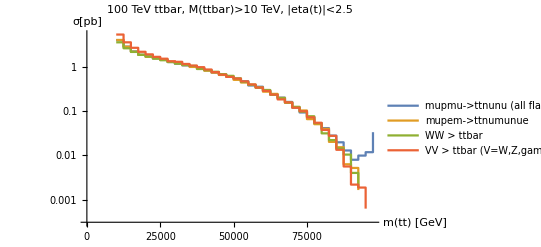

```mathematica
ListLogPlot[{mumuttbar,muettbar,WWttbar,VVttbar},InterpolationOrder->0,Joined->True,PlotLabel->"100 TeV ttbar, M(ttbar)>10 TeV, |eta(t)|<2.5", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

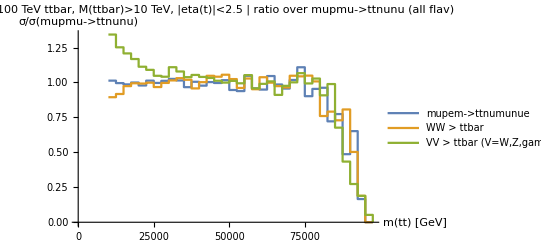

```mathematica
ListPlot[{rapp[muettbar,mumuttbar],rapp[WWttbar,mumuttbar],rapp[VVttbar,mumuttbar]},InterpolationOrder->0,Joined->True,PlotLabel->"100 TeV ttbar, M(ttbar)>10 TeV, |eta(t)|<2.5 | ratio over mupmu->ttnunu (all flav)", PlotLegends->{"mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupmu->ttnunu)"}]
```

```mathematica
namerun="centoTeVnocuts"
namerun="centoTeVcutMttventiTeV"
```

centoTeVnocuts

centoTeVcutMttventiTeV

```mathematica
namefolder="mumu_to_tt_vuvu_massivemu";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
mumuttbar =.
mumuttbar =prova[8];
```

```mathematica
namefolder="mupem_to_tt_vumuvue_massivemuande";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
muettbar=.
muettbar =prova[8];
```

```mathematica
namefolder="WW_to_tt_massivemu";
prova=.

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
WWttbar =.
WWttbar =prova[8];
```

```mathematica
namefolder="VV_to_tt_massivemu";

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
VVttbar =.
VVttbar =prova[8];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_M},{9_DELTAR}}

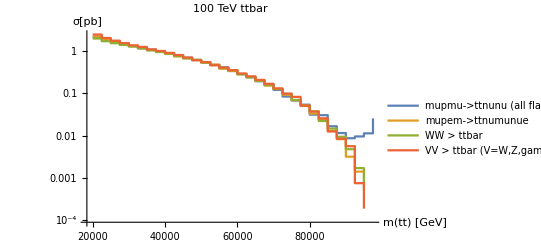

```mathematica
ListLogPlot[{mumuttbar,muettbar,WWttbar,VVttbar},InterpolationOrder->0,Joined->True,PlotLabel->"100 TeV ttbar", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

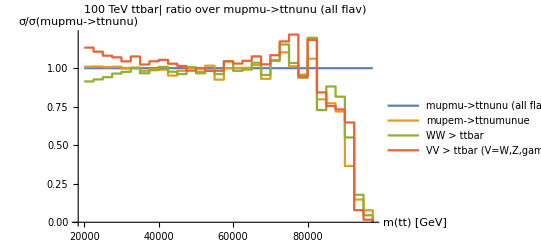

```mathematica
ListPlot[{rapp[mumuttbar,mumuttbar],rapp[muettbar,mumuttbar],rapp[WWttbar,mumuttbar],rapp[VVttbar,mumuttbar]},InterpolationOrder->0,Joined->True,PlotLabel->"100 TeV ttbar| ratio over mupmu->ttnunu (all flav)", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupmu->ttnunu)"}]
```

```mathematica
namerun="mttminhalfSunotevnocuts"
namerun="mttminhalfStretevnocuts"
namerun="mttminhalfSdiecitevnocuts"
namerun="mttminhalfScentotevnocutsmoltofine" (*only for this set plotnumber=9*)
```

mttminhalfSunotevnocuts

mttminhalfStretevnocuts

mttminhalfSdiecitevnocuts

mttminhalfScentotevnocutsmoltofine

```mathematica
namerun="unotevnocuts"
namerun="tretevnocuts"
namerun="diecitevnocuts"
namerun="centotevnocutsmoltofine"
```

unotevnocuts

tretevnocuts

diecitevnocuts

centotevnocutsmoltofine

```mathematica
namerun="centotevrapdueemezzo"
namerun="unotevrapdueemezzo"
namerun="tretevrapdueemezzo"
namerun="diecitevrapdueemezzo"
```

centotevrapdueemezzo

unotevrapdueemezzo

tretevrapdueemezzo

diecitevrapdueemezzo

```mathematica
nbintogether=4;
plotnumber=8;
```

```mathematica
namesruns={"centotevrapdueemezzo"
,"unotevrapdueemezzo"
,"tretevrapdueemezzo"
,"diecitevrapdueemezzo"
,"unotevnocuts"
,"tretevnocuts"
,"diecitevnocuts"
,"centotevnocutsmoltofine"
,"mttminhalfSunotevnocuts"
,"mttminhalfStretevnocuts"
,"mttminhalfSdiecitevnocuts"
,"mttminhalfScentotevnocutsmoltofine" (*only for this set plotnumber=9*)}
```

{centotevrapdueemezzo,unotevrapdueemezzo,tretevrapdueemezzo,diecitevrapdueemezzo,unotevnocuts,tretevnocuts,diecitevnocuts,centotevnocutsmoltofine,mttminhalfSunotevnocuts,mttminhalfStretevnocuts,mttminhalfSdiecitevnocuts,mttminhalfScentotevnocutsmoltofine}

```mathematica
Do[

nbintogether=4;
plotnumber=8;



namerun=namesruns[[i]];

subdir="nocuts";
Which[StringMatchQ[namesruns[[i]],"*rapdueemezzo*"],subdir="rapdueemezzo",
StringMatchQ[namesruns[[i]],"*mttminhalfS*"],subdir="mttminhalfS"
];


Which[StringMatchQ[namesruns[[i]],"*uno*"],nbintogether=1,
StringMatchQ[namesruns[[i]],"*tre*"],nbintogether=4,
StringMatchQ[namesruns[[i]],"*dieci*"],nbintogether=10,
StringMatchQ[namesruns[[i]],"*cento*"],nbintogether=40];

If[ namesruns[[i]]=="mttminhalfScentotevnocutsmoltofine",plotnumber=9];



namefolder="mumu_to_tt_vuvu_massivemu";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
mumuttbar =.;
mumuttbar =joinbin[prova[plotnumber],nbintogether];


namefolder="mupem_to_tt_vumuvue_massivemuande";
NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
muettbar=.;
muettbar =joinbin[prova[plotnumber],nbintogether];


namefolder="WW_to_tt_massivemu";
prova=.;

NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
WWttbar =.;
WWttbar =joinbin[prova[plotnumber],nbintogether];


namefolder="VV_to_tt_massivemu";

NameH=.;
NH=.;
Estrai["/Users/pagani/mu-vbf/DavideMG5Runs/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH];
VVttbar =.;
VVttbar =joinbin[prova[plotnumber],nbintogether];
NameH;

mainpanel=ListLogLogPlot[{mumuttbar,muettbar,WWttbar,VVttbar},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ[pb]"}];

ratioinset=ListLogLinearPlot[{rapp[mumuttbar,mumuttbar],rapp[muettbar,mumuttbar],rapp[WWttbar,mumuttbar],rapp[VVttbar,mumuttbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupmu->ttnunu (all flav)", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupmu->ttnunu)"}];


ratioinset2=ListLogLinearPlot[{rapp[mumuttbar, muettbar],rapp[muettbar, muettbar],rapp[WWttbar, muettbar],rapp[VVttbar, muettbar]},InterpolationOrder->0,Joined->True,PlotLabel->"ttbar| ratio over mupem->ttnumunue", PlotLegends->{"mupmu->ttnunu (all flav)","mupem->ttnumunue ","WW > ttbar", "VV > ttbar (V=W,Z,gamma)"},AxesLabel->{"m(tt) [GeV]","σ/σ(mupem->ttnumunue)"}];

Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/1stroundofplots/"<>subdir<>"/"<>namerun<>"_absolute.pdf",mainpanel];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/1stroundofplots/"<>subdir<>"/"<>namerun<>"_ratio.pdf",ratioinset];
Export["/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/1stroundofplots/"<>subdir<>"/"<>namerun<>"_ratio2.pdf",ratioinset2];
"/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/1stroundofplots/unotevrapdueemezzo_absolute.pdf"
"/Users/pagani/mu-vbf/DavideMG5Runs/Plots/ttbar/1stroundofplots/unotevrapdueemezzo_ratio.pdf"




,{i,1,Length[namesruns]}]
```

Unset::write: Tag Times in Null {{50925.,0.423132},{52925.,0.390404},{54925.,0.351559},{56925.,0.315852},{58925.,0.274541},{60925.,0.24588},{62925.,0.210621},{64925.,0.18244},{66925.,0.149456},{68925.,0.131074},«15»} is Protected.

Unset::write: Tag Times in Null {{50925.,0.425979},{52925.,0.3944},{54925.,0.34429},{56925.,0.311216},{58925.,0.276647},{60925.,0.236814},{62925.,0.204301},{64925.,0.179822},{66925.,0.156807},{68925.,0.126411},«15»} is Protected.

Unset::write: Tag Times in Null {{185.,72.8575},{585.,696.41},{985.,295.372},{1385.,142.605},{1785.,74.9454},{2185.,45.3498},{2585.,28.705},{2985.,19.7839},{3385.,13.9875},{3785.,10.6147},«15»} is Protected.

General::stop: Further output of Unset::write will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
StringMatchQ["centoaldofdas","*cento*"]
```

True